```mathematica
ResourceFunction["MaTeXInstall"][];
ConfigureMaTeX["pdfLaTeX" -> "/usr/local/bin/pdflatex"];
```

```mathematica
Needs["MaTeX`"]
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color}"}];
```

## Energy control

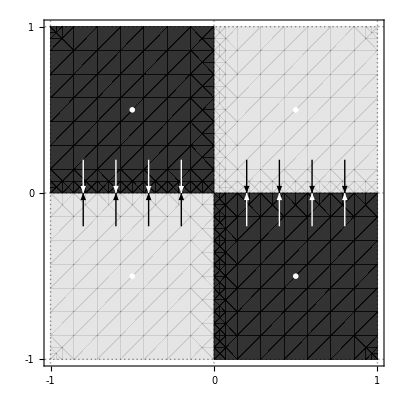

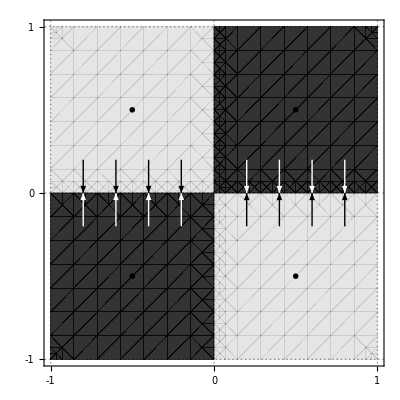

```mathematica
energyControl1 = ContourPlot[x*y, {x, -1, 1}, {y, -1, 1},
Contours->1,
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
PlotRange->{1, -1},
FrameLabel ->{MaTeX["\\dot \\theta",Magnification->1.5],MaTeX[ "E",Magnification->1.5]},
FrameTicks->{{0, -1, 1}, {0, -1, 1}},
FrameTicksStyle->Directive[FontSize->16],
GridLines->{{0, -1, 1}, {0, -1, 1}},
Method->{"TransparentPolygonMesh"->True},
Epilog->{
White,
Text[MaTeX["+a_{max}",Magnification->2], {.5, .5}],Text[MaTeX["+a_{max}",Magnification->2], {-.5, -.5}],
Text[MaTeX["\\color{white}-a_{max}",Magnification->2], {.5, -.5}],
Text[MaTeX["\\color{white}-a_{max}",Magnification->2], {-.5, .5}],
Table[Arrow[{{i, .2}, {i, 0}}], {i, -.8, -.2, .2}],
Table[Arrow[{{i, -.2}, {i, 0}}], {i, .8, .2, -.2}],
Black,
Table[Arrow[{{i, .2}, {i, 0}}], {i, .8, .2, -.2}],
Table[Arrow[{{i, -.2}, {i, 0}}], {i, -.8, -.2, .2}]
}
]

energyControl2 = ContourPlot[-x*y, {x, -1, 1}, {y, -1, 1},
Contours->1,
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
PlotRange->{1, -1},
FrameLabel ->{MaTeX["\\dot \\theta",Magnification->1.5],MaTeX[ "E",Magnification->1.5]},
FrameTicks->{{0, -1, 1}, {0, -1, 1}},
FrameTicksStyle->Directive[FontSize->16],
GridLines->{{0, -1, 1}, {0, -1, 1}},
Method->{"TransparentPolygonMesh"->True},
Epilog->{
Black,
Text[MaTeX["+a_{max}",Magnification->2], {-.5, .5}],Text[MaTeX["+a_{max}",Magnification->2], {.5, -.5}],
Text[MaTeX["\\color{white}-a_{max}",Magnification->2], {.5, .5}],
Text[MaTeX["\\color{white}-a_{max}",Magnification->2], {-.5, -.5}],
Table[Arrow[{{i, .2}, {i, 0}}], {i, -.8, -.2, .2}],
Table[Arrow[{{i, -.2}, {i, 0}}], {i, .8, .2, -.2}],
White,
Table[Arrow[{{i, .2}, {i, 0}}], {i, .8, .2, -.2}],
Table[Arrow[{{i, -.2}, {i, 0}}], {i, -.8, -.2, .2}]
}
]
```

```mathematica
Export[NotebookDirectory[]<>"../energy-control1.pdf",energyControl1,"PDF"]
Export[NotebookDirectory[]<>"../energy-control2.pdf",energyControl2,"PDF"]
```

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../energy-control1.pdf

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../energy-control2.pdf

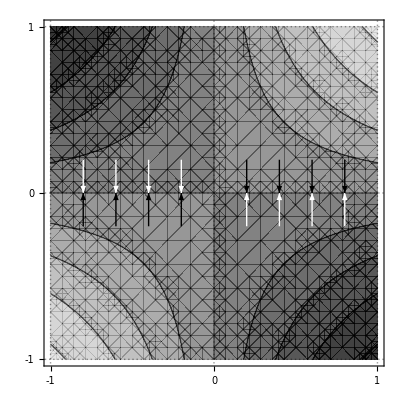

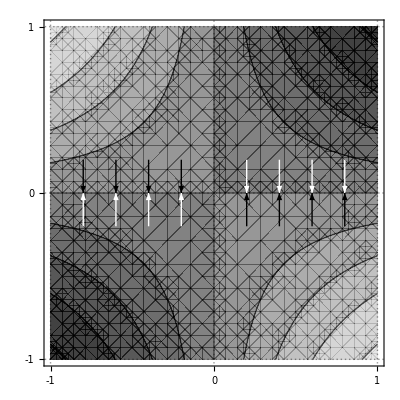

```mathematica
energyControl3 = ContourPlot[Tanh[x*y], {x, -1, 1}, {y, -1, 1},
Contours->10,
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
PlotRange->{1, -1},
FrameLabel ->{MaTeX["\\dot \\theta",Magnification->1.5],MaTeX[ "E",Magnification->1.5]},
FrameTicks->{{0, -1, 1}, {0, -1, 1}},
FrameTicksStyle->Directive[FontSize->16],
GridLines->{{0, -1, 1}, {0, -1, 1}},
Method->{"TransparentPolygonMesh"->True},
Epilog->{
White,
Table[Arrow[{{i, .2}, {i, 0}}], {i, -.8, -.2, .2}],
Table[Arrow[{{i, -.2}, {i, 0}}], {i, .8, .2, -.2}],
Black,
Table[Arrow[{{i, .2}, {i, 0}}], {i, .8, .2, -.2}],
Table[Arrow[{{i, -.2}, {i, 0}}], {i, -.8, -.2, .2}]
}
]

energyControl4 = ContourPlot[-Tanh[x*y], {x, -1, 1}, {y, -1, 1},
Contours->10,
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
PlotRange->{1, -1},
FrameLabel ->{MaTeX["\\dot \\theta",Magnification->1.5],MaTeX[ "E",Magnification->1.5]},
FrameTicks->{{0, -1, 1}, {0, -1, 1}},
FrameTicksStyle->Directive[FontSize->16],
GridLines->{{0, -1, 1}, {0, -1, 1}},
Method->{"TransparentPolygonMesh"->True},
Epilog->{
Black,
Table[Arrow[{{i, .2}, {i, 0}}], {i, -.8, -.2, .2}],
Table[Arrow[{{i, -.2}, {i, 0}}], {i, .8, .2, -.2}],
White,
Table[Arrow[{{i, .2}, {i, 0}}], {i, .8, .2, -.2}],
Table[Arrow[{{i, -.2}, {i, 0}}], {i, -.8, -.2, .2}]
}
]
```

```mathematica
Export[NotebookDirectory[]<>"../energy-control3.pdf",energyControl3,"PDF"]
Export[NotebookDirectory[]<>"../energy-control4.pdf",energyControl4,"PDF"]
```

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../energy-control3.pdf

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../energy-control4.pdf

## Cogging Torque

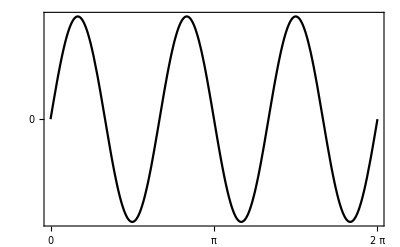

```mathematica
coggingTorque = Plot[Sin[3*x], {x, 0, 2Pi},
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
PlotLegends->{Placed[LineLegend[{MaTeX[TeXForm[Subscript[τ, c]],Magnification->2]}], {.85, .9}]},
PlotRange->{5, -5},
FrameLabel ->{MaTeX["\\text{Angolo}",Magnification->1.5], MaTeX["\\text{Coppia}",Magnification->1.5]},
FrameTicks->{{{0}, None}, {{0, Pi, 2Pi}, None}},
FrameTicksStyle->Directive[FontSize->16],
GridLines->{{0, Pi, 2Pi}, {0}}
]
```

```mathematica
Export[NotebookDirectory[]<>"../cogging-torque.pdf",coggingTorque,"PDF"]
```

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../cogging-torque.pdf

## Parametri motore

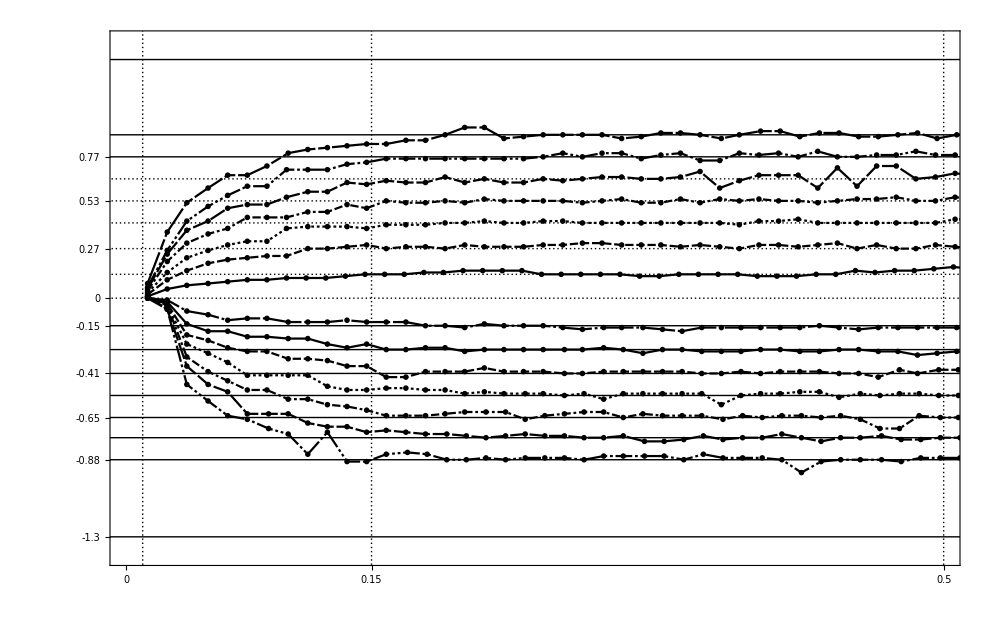

```mathematica
data = {};
plotLegend = {};
For [i = 3, i < 10, i++,
AppendTo[data, Import[NotebookDirectory[]<>"../../data/calibration/"<>ToString[i]<>".csv"]];
AppendTo[plotLegend,MaTeX[ToString[i*15 //IntegerPart]<>"", Magnification->1.5]];
];
For [i = 3, i < 10, i++,
AppendTo[data, Import[NotebookDirectory[]<>"../../data/calibration/"<>ToString[-i]<>".csv"]];
AppendTo[plotLegend,MaTeX[ToString[-i*15 //IntegerPart]<>"", Magnification->1.5]];
];

motorPlot1 = ListLinePlot[
data,
InterpolationOrder->1,
PlotRange->{{0, .5}, {-1.4, 1.4}},
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
ImageSize->{1000, 500},
PlotLegends->Placed[
LineLegend[plotLegend,LegendLayout->(Grid@Transpose@Partition[Row/@#,7]&)],Right
],
FrameTicksStyle->Directive[FontSize->16],
FrameTicks->{{{0, .13, .27, .41, .53, .65, .77, .89, -.15, -.28, -.41, -.53, -.65, -.76, -.88, 1.3, -1.3}, None}, {0, .15, .5}},
GridLines->{{0.01, .15, .5}, {0, .13, .27, .41, .53, .65, .77, .89, -.15, -.28, -.41, -.53, -.65, -.76, -.88, 1.3, -1.3} },
FrameLabel ->{MaTeX["\\text{Tempo }(s)",Magnification->1.5], MaTeX["\\text{Velocità }(m/s)",Magnification->1.5]}
]
```

```mathematica
Export[NotebookDirectory[]<>"../motor-vmax-fit.pdf",motorPlot1,"PDF"]
```

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../motor-vmax-fit.pdf

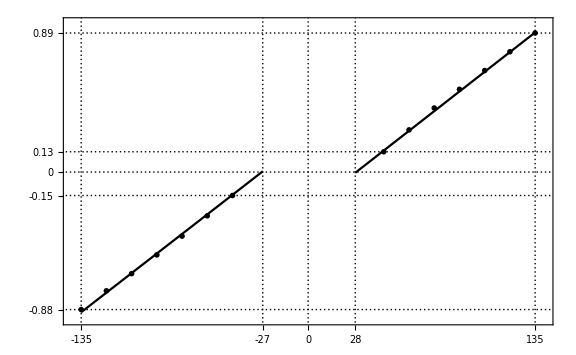

```mathematica
lineFitData = { 
{-135, -.88},
{-120, -.76},
{-105, -.65},
{-90, -.53},
{-75, -.41},
{-60, -.28},
{-45, -.15},
{45, .13},
{60, .27},
{75, .41},
{90, .53},
{105, .65},
{120, .77},
{135, .89},
};

listPltot1= ListPlot[
lineFitData,
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid", "Large"},
FrameTicksStyle->Directive[FontSize->16],
FrameLabel ->{MaTeX["\\text{PWM}",Magnification->1.5], MaTeX["\\text{Velocità massima }\\left(\\frac m s\\right)",Magnification->1.5]},
FrameTicks->{{{0,.89, -.88, .13, -.15}, None}, {0, -135, 135, -27, 28}},
GridLines->{{0, -135, 135, -27, 28}, {0, .89, -.88, .13, -.15} },
PlotRange->{{-140, 140}, {-.94, .95}}
];

linePlot1 = Plot[.00835x + .23, {x, -135, -27}, PlotTheme->"Monochrome"];
linePlot2 = Plot[.00840x - .24, {x, 28, 135}, PlotTheme->"Monochrome",  PlotLegends->{MaTeX["v_{\\infty}(u) = \\left\\{\\begin{aligned} .00835u &+ .23, \\ u < -27 \\\\ .00840u &- .24 , \\ u > 28\\end{aligned} \\right.", Magnification->1.5]}];
motorPlot2 = Show[listPltot1, linePlot1, linePlot2]
```

```mathematica
Export[NotebookDirectory[]<>"../motor-offset.pdf",motorPlot2,"PDF"]
B=120
```

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../motor-offset.pdf

120

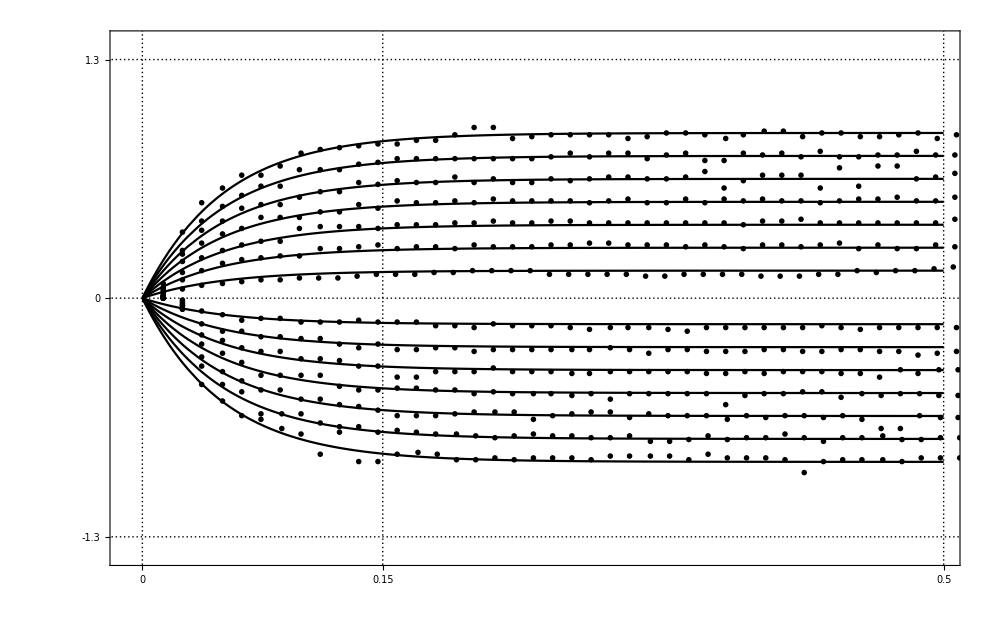

```mathematica
data = {};
plotLegend = {};
For [i = 3, i < 10, i++,
AppendTo[data, Import[NotebookDirectory[]<>"../../data/calibration/"<>ToString[i]<>".csv"]];
AppendTo[plotLegend,MaTeX[ToString[i*15 //IntegerPart]<>"", Magnification->1.5]];
];
For [i = 3, i < 10, i++,
AppendTo[data, Import[NotebookDirectory[]<>"../../data/calibration/"<>ToString[-i]<>".csv"]];
AppendTo[plotLegend,MaTeX[ToString[-i*15 //IntegerPart]<>"", Magnification->1.5]];
];

listPlot2 = ListPlot[
data,
InterpolationOrder->1,
PlotRange->{{-.01, .5}, {-1.4, 1.4}},
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
ImageSize->{1000, 500},
PlotLegends->Placed[
LineLegend[plotLegend,LegendLayout->(Grid@Transpose@Partition[Row/@#,7]&)],Right
],
FrameTicksStyle->Directive[FontSize->16],
FrameTicks->{{{0, 1.3, -1.3}, None}, {0, .15, .5}},
GridLines->{{0, .15, .5}, {0, 1.3, -1.3} },
FrameLabel ->{MaTeX["\\text{Tempo }(s)",Magnification->1.5], MaTeX["\\text{Velocità }\\left(\\frac m s\\right)",Magnification->1.5]}
];

B=120;
tau=20;
expoPlots = {};
For [i = 3, i < 10, i++,
AppendTo[
expoPlots,
Plot[If[x > 0, (i*15/B-27/B)(1-E^-(tau x)), -10], {x, -.1, .5}, PlotTheme->"Monochrome"]
];
];
For [i = 3, i < 10, i++,
AppendTo[
expoPlots,
Plot[If[x > 0, (-i*15/B+28/B)(1-E^-(tau x)), 10], {x, -.1, .5}, PlotTheme->"Monochrome"]
]
];


motorPlot3 = Show[listPlot2, expoPlots]
```

```mathematica
Export[NotebookDirectory[]<>"../motor-expo-fit.pdf",motorPlot3,"PDF"]
Solve[B/(a M) == tau, a] /. params
```

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../motor-expo-fit.pdf

ReplaceAll::reps: {params} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{{a→6/M}}/.params

## Grafici simulazioni

Per usare questi grafici è necessario aprire il "notebook dei calcoli"/Users/matteo/repo/uni/dpic/docs/report/assets/source/calcoli.nbNone/Users/matteo/repo/uni/dpic/docs/report/assets/source/calcoli.nb ed eseguire il codice, in modo che siano definite le funzioni corrette.

0.0243628 (1-Cos[θ[t]])+0.105 x'[t]^2+0.000039541 θ'[t]^2+0.011 (0.012769 Sin[θ[t]]^2 θ'[t]^2+(x'[t]+0.113 Cos[θ[t]] θ'[t])^2)

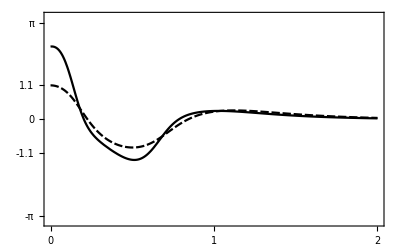

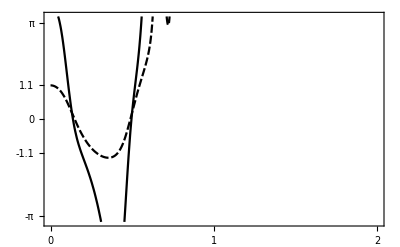

LQRegulatorGains::invsys3: ssm/.params is not a valid StateSpaceModel, AffineStateSpaceModel, or NonlinearStateSpaceModel.

ReplaceAll::reps: {params} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

LQRegulatorGains::invsys3: ssm/.params is not a valid StateSpaceModel, AffineStateSpaceModel, or NonlinearStateSpaceModel.

ReplaceAll::reps: {params} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

g l m (1-Cos[θ[t]])+1/2 M x'[t]^2+1/2 (J-l^2 m) θ'[t]^2+1/2 m (l^2 Sin[θ[t]]^2 θ'[t]^2+(x'[t]+l Cos[θ[t]] θ'[t])^2)/.params

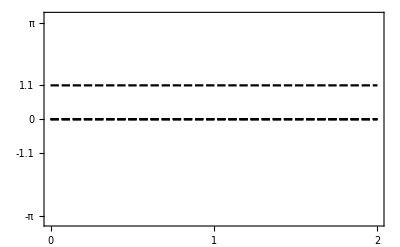

-Graphics-

```mathematica
s[t_]:= {x[t],  x'[t], θ[t], θ'[t] };
T = 2;

Klqr1 = LQRegulatorGains[ssm /. params, {Q, R} /. {r11->1, q11->1} /. params];
solutionsLQR1 = simulateSystem[-Klqr1.s[t], T, {0, 0, 1.1,0}];

Klqr2 = LQRegulatorGains[ssm /. params, {Q, R} /. {r11->.1, q11->1} /. params];
solutionsLQR2 = simulateSystem[-Klqr2.s[t], T, {0, 0, 1.1,0}];

v2 = (x'[t] + l θ'[t]*Cos[θ[t]])^2 + ( l θ'[t]*Sin[θ[t]])^2;
Kin = 1/2 *M*x'[t]^2       + 1/2* m*v2    + 1/2*(J - m l^2)*θ'[t]^2 ;
V = m*g*l*(1-Cos[θ[t]]);
Energy = Kin + V /. params


occBlowup1= Plot[{
-Klqr1.solutionsLQR1/Pi,
solutionsLQR1[[3]]
},
{t, 0, T},
PlotRange->{-Pi-.2, Pi+.2},
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
PlotLegends->{MaTeX["f_{LQR}\\left(N /\pi\\right)",Magnification->1.5],MaTeX["\\theta_{LQR}",Magnification->1.5]},
FrameTicks->{{{0, Pi, -Pi, -1.1, 1.1}, None}, {{0, 1, 2}, None}},
GridLines->{{0,1, 2}, {0, Pi, -1.1, 1.1, -Pi} },
FrameTicksStyle->Directive[FontSize->13],
FrameLabel ->{MaTeX["\\text{Tempo }(s)",Magnification->1.5]}
]

occBlowup2= Plot[{
-Klqr2.solutionsLQR2/Pi,
solutionsLQR2[[3]]
},
{t, 0, T},
PlotRange->{-Pi-.2, Pi+.2},
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
PlotLegends->{MaTeX["f_{LQR}\\left(N /\pi\\right)",Magnification->1.5],MaTeX["\\theta_{LQR}",Magnification->1.5]},
FrameTicks->{{{0, Pi, -Pi, -1.1, 1.1}, None}, {{0, 1, 2}, None}},
GridLines->{{0,1, 2}, {0, Pi, -1.1, 1.1, -Pi} },
FrameTicksStyle->Directive[FontSize->13],
FrameLabel ->{MaTeX["\\text{Tempo }(s)",Magnification->1.5]}
]
(*
energyPlot= Plot[{
Energy /.{x[t] -> solutionsLQR1[[1]], x'[t]->solutionsLQR1[[2]], θ[t]->solutionsLQR1[[3]], θ'[t]->solutionsLQR1[[4]]},
Energy /.{x[t] -> solutionsLQR2[[1]], x'[t]->solutionsLQR2[[2]], θ[t]->solutionsLQR2[[3]], θ'[t]->solutionsLQR2[[4]]}
},
{t, 0, T},
PlotRange->{-Pi-.2, Pi+.2},
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
PlotLegends->{MaTeX["f_{LQR}\\left(N /\pi\\right)",Magnification->1.5],MaTeX["\\theta_{LQR}(rad)",Magnification->1.5]},
FrameTicks->{{{0, Pi, -Pi, -1, 1}, None}, {{0, 1, 2}, None}},
GridLines->{{0,1, 2}, {0, Pi, -1, 1, -Pi} },
FrameTicksStyle->Directive[FontSize->13],
FrameLabel ->{MaTeX["\\text{Tempo }(s)",Magnification->1.5]}
]*)
```

```mathematica
series = Series[motionEquations[[2, 2]], {θ[t], 0, 3}] /. {u[t]->0, θ'[t]->0} /. params
Solve[(Energy /. {x[t] -> 0, x'[t]->0, θ[t]->1, θ'[t]->0}) == (Energy /. {x[t] -> 0, x'[t]->0, θ[t]->0, θ'[t]->s}),s] 
Energy /. {x[t] -> 0, x'[t]->0, θ[t]->1, θ'[t]->0}
Export[NotebookDirectory[]<>"../occasional-blowup-r1.pdf",occBlowup1,"PDF"]
Export[NotebookDirectory[]<>"../occasional-blowup-r.1.pdf",occBlowup2,"PDF"]
```

73.0823 θ[t]-18.0204 θ[t]^3+O[θ[t]]^4

{{s→-7.88794},{s→7.88794}}

0.0111995

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../occasional-blowup-r1.pdf

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../occasional-blowup-r.1.pdf

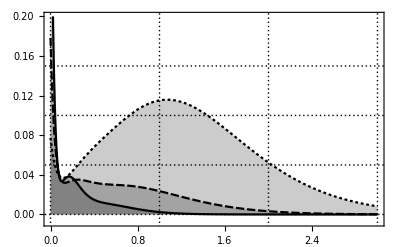

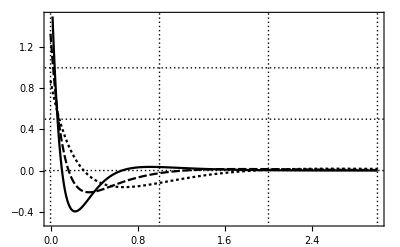

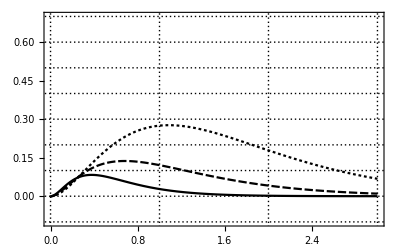

```mathematica
s[t_]:= {x[t],  x'[t], θ[t], θ'[t] };
T = 3;

Klqr = LQRegulatorGains[ssm /. params, {Q, R} /. params];
solutionsLQR = simulateSystem[-Klqr.s[t], T, {0, 0, .2 ,0}];

Krandom = StateFeedbackGains[ssm /. params, {-8.5 , -8.4, -1.8, -1.9}];
solutionsRandom = simulateSystem[-Krandom.s[t], T, {0, 0, .2,0}];

Krandom2 = StateFeedbackGains[ssm /. params, {-2, -2.1, -10.3, -1.4}];
solutionsRandom2 = simulateSystem[-Krandom2.s[t], T, {0, 0, .2,0}];


opt1 = Plot[{
costIntegrand[t, -Klqr.solutionsLQR, solutionsLQR],
costIntegrand[t, -Krandom.solutionsRandom, solutionsRandom],
costIntegrand[t, -Krandom2.solutionsRandom2, solutionsRandom2]
},
{t, 0, T},
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
Filling->Axis,
PlotRange->{-.0075, .2},
GridLines->{{0,1 , 2, 3, 4, 5}, {0, .05,.1, .15}},
PlotLegends->{MaTeX["K_{LQR}",Magnification->1.5],MaTeX["K_{1}",Magnification->1.5],MaTeX["K_{2}",Magnification->1.5]},
FrameTicksStyle->Directive[FontSize->13],
FrameLabel ->{MaTeX["\\text{Tempo }(s)",Magnification->1.5], MaTeX["\\text{Costo istantaneo}",Magnification->1.5]}
]

opt2 = Plot[{
 -Klqr.solutionsLQR,

 -Krandom.solutionsRandom,

-Krandom2.solutionsRandom2
},
{t, 0, T},
PlotRange->{-.5, 1.5},
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
GridLines->{{0,1 , 2, 3, 4, 5}, {0, .5, 1}},
PlotLegends->{MaTeX["f_{LQR}",Magnification->1.5],MaTeX["f_{1}",Magnification->1.5],MaTeX["f_{2}",Magnification->1.5]},
FrameTicksStyle->Directive[FontSize->13],
FrameLabel ->{MaTeX["\\text{Tempo }(s)",Magnification->1.5], MaTeX["\\text{Forza subita }(N)",Magnification->1.5]}
]

opt3 = Plot[{
solutionsLQR[[1]],
 solutionsRandom[[1]],
solutionsRandom2[[1]]
},
{t, 0, T},
PlotRange->{-.1, .7},
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
GridLines->{{0,1 , 2, 3, 4, 5}, {0, .1, .2, .3,.4, .5, .6, .7, -.1}},
PlotLegends->{MaTeX["q_{LQR}",Magnification->1.5],MaTeX["q_{1}",Magnification->1.5],MaTeX["q_{2}",Magnification->1.5]},
FrameTicksStyle->Directive[FontSize->13],
FrameLabel ->{MaTeX["\\text{Tempo }(s)",Magnification->1.5], MaTeX["\\text{Posizione }(m)",Magnification->1.5]}
]
```

```mathematica
(*Ottimalità*)
Q //MatrixForm
DiscreteLQRegulatorGains[ssm /. params, {Q, R} /. params, .005]
params
A-B.Klqr /. params //Eigenvalues
Jlqr = NIntegrate[costIntegrand[t, -Klqr.solutionsLQR, solutionsLQR], {t, 0, T}];
Jrandom1 = NIntegrate[costIntegrand[t, -Krandom.solutionsRandom, solutionsRandom], {t, 0, T}];
Jrandom2 = NIntegrate[costIntegrand[t, -Krandom.solutionsRandom2, solutionsRandom2], {t, 0, T}];
Jrandom1/Jlqr
Jrandom2/Jlqr

Export[NotebookDirectory[]<>"../opt1.pdf",opt1,"PDF"]
Export[NotebookDirectory[]<>"../opt2.pdf",opt2,"PDF"]
Export[NotebookDirectory[]<>"../opt3.pdf",opt3,"PDF"]
(*todo print graphs*)
```

(q11 | 0 | 0 | 0
0 | m+M | 0 | l m
0 | 0 | g l m | 0
0 | l m | 0 | J)

{{-3.62988,-2.77128,-9.88987,-1.18201}}

{g→9.8,l→0.113,m→0.022,M→0.21,J→0.00036,r11→0.1,q11→1.5}

{-8.8427,-8.59019,-5.73433,-2.80091}

1.81346

7.86255

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../opt1.pdf

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../opt2.pdf

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../opt3.pdf

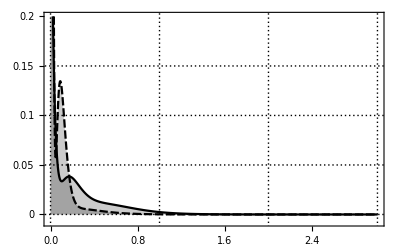

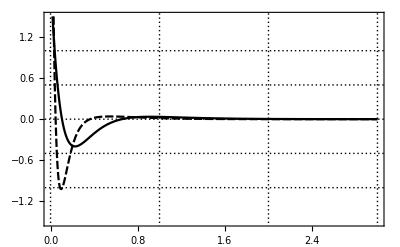

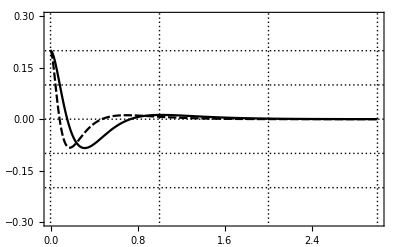

```mathematica
s[t_]:= {x[t],  x'[t], θ[t], θ'[t] };
T = 3;

Klqr = LQRegulatorGains[ssm /. params, {Q, R} /. params];
solutionsLQR = simulateSystem[-Klqr.s[t], T, {0, 0, .2 ,0}];

Kfast = StateFeedbackGains[ssm /. params, {-4, -5, -20, -21}];
solutionsFast = simulateSystem[-Kfast.s[t], T, {0, 0, .2 ,0}];


nopt1= Plot[{
costIntegrand[t, -Klqr.solutionsLQR, solutionsLQR],
costIntegrand[t, -Kfast.solutionsFast, solutionsFast]
},
{t, 0,T},
PlotRange->{-.0075, .2},
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
Filling->Axis,
PlotLegends->{MaTeX["K_{LQR}",Magnification->1.5],MaTeX["K_{fast}",Magnification->1.5]},
GridLines->{{0,1 , 2, 3, 4, 5}, {0, .05, .1, .15}},
FrameTicks->{{{0, .05, .1, .15, .2}, None}, {Automatic, None}},
FrameTicksStyle->Directive[FontSize->13],
FrameLabel ->{MaTeX["\\text{Tempo }(s)",Magnification->1.5], MaTeX["\\text{Costo istantaneo}",Magnification->1.5]}
]

nopt2 = Plot[{
 -Klqr.solutionsLQR,

 -Kfast.solutionsFast
},
{t, 0, T},
PlotRange->{-1.5, 1.5},
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
PlotLegends->{MaTeX["f_{LQR}",Magnification->1.5],MaTeX["f_{fast}",Magnification->1.5]},
GridLines->{{0,1 , 2, 3, 4, 5}, {0, .5, 1, -.5, -1}},
FrameTicksStyle->Directive[FontSize->13],
FrameLabel->{MaTeX["\\text{Tempo }(s)",Magnification->1.5],MaTeX["\\text{Forza subita }(N)",Magnification->1.5]}
]

nopt3 = Plot[{
solutionsLQR[[3]],
 solutionsFast[[3]]
},
{t, 0, T},
PlotRange->{-.3, .3},
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
PlotLegends->{MaTeX["q_{LQR}",Magnification->1.5],MaTeX["q_{fast}",Magnification->1.5]},
GridLines->{{0,1 , 2, 3, 4, 5}, {0, .1, .2, -.1, -.2}},
FrameTicksStyle->Directive[FontSize->13],
FrameLabel->{MaTeX["\\text{Tempo }(s)",Magnification->1.5],MaTeX["\\text{Posizione }(m)",Magnification->1.5]}
]
```

```mathematica
(*Aha questa funzione è più fast*)
Eigenvalues[A-B.K] /. params

Jlqr = NIntegrate[costIntegrand[t, -Klqr.solutionsLQR, solutionsLQR], {t, 0, T}];
Jfast = NIntegrate[costIntegrand[t, -Kfast.solutionsFast, solutionsFast], {t, 0, T}];
Jfast/Jlqr

Export[NotebookDirectory[]<>"../nopt1.pdf",nopt1,"PDF"]
Export[NotebookDirectory[]<>"../nopt2.pdf",nopt2,"PDF"]
Export[NotebookDirectory[]<>"../nopt3.pdf",nopt3,"PDF"]
(*todo print graphs*)
```

{-8.55825-0.0184522 ⅈ,-8.55825+0.0184522 ⅈ,-1.79823-1.03305 ⅈ,-1.79823+1.03305 ⅈ}

2.23318

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../nopt1.pdf

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../nopt2.pdf

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../nopt3.pdf

108

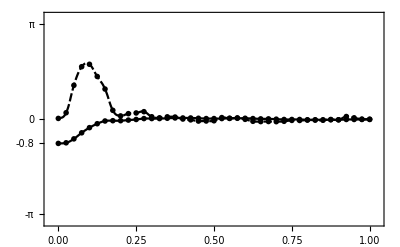

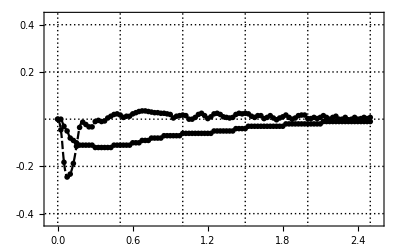

```mathematica
data = {
Import[NotebookDirectory[]<>"../../data/good-theta-max/.8.csv"],
Import[NotebookDirectory[]<>"../../data/good-theta-max/.9.csv"],
Import[NotebookDirectory[]<>"../../data/good-theta-max/1.csv"]
} ;

time108 = Table[.025*i, {i, 0, 107, 1}];

ltheta8 =  Transpose[data[[1]]][[1;;4]] * { 1, 1/4,1, 1/4};
ltheta8[[1]] //Length
 thetaPlot8 = ListLinePlot[
{
Transpose[{
time108,
-ltheta8[[3]]
}][[1;; 41]],
Transpose[{
time108,
-ltheta8[[4]]
}][[1;; 41]]
},
InterpolationOrder->2,
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
FrameTicksStyle->Directive[FontSize->16],
FrameLabel ->{MaTeX["\\text{Tempo }(s)",Magnification->1.5]},
PlotLegends->{MaTeX["\\theta",Magnification->1.5],MaTeX["\\dot \\theta \\left(s^{-1} / 4\\right)",Magnification->1.5]},
FrameTicks->{{{-Pi, Pi, -.8, 0}, None}, {Automatic, None}},
PlotRange->{{-.025, 1.025},{-Pi-.25, Pi+.25}},
GridLines->{{-.03, 0, .2, .4, .6, .8, 1}, {0,-.8, Pi, -Pi}}
]

xPlot8 = ListLinePlot[{
Transpose[{
time108,
-ltheta8[[1]]
}][[1;;101]],
Transpose[{
time108,
-ltheta8[[2]]
}][[1;;101]]
},
InterpolationOrder->2,
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
FrameTicksStyle->Directive[FontSize->16],
FrameLabel ->{MaTeX["\\text{Tempo }(s)",Magnification->1.5]},
PlotLegends->{MaTeX["q(m)",Magnification->1.5],MaTeX["\\dot q \\left(ms^{-1}/ 4\\right) ",Magnification->1.5]},
PlotRange->{{-.0575, 2.5575},{-.435, .435}},
FrameTicks->{{{-.4, .4, .2, -.2}, None}, {Automatic, None}},
GridLines->{{-.25, 0, .5, 1, 1.5, 2, 2.5}, {0, .2, -.2, -.4, .4}}
]
```

121

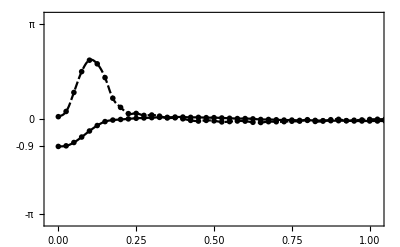

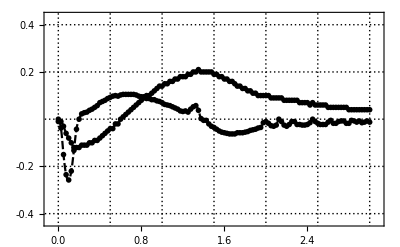

```mathematica
data = {
Import[NotebookDirectory[]<>"../../data/good-theta-max/.8.csv"],
Import[NotebookDirectory[]<>"../../data/good-theta-max/.9.csv"],
Import[NotebookDirectory[]<>"../../data/good-theta-max/1.csv"]
} ;

time121 = Table[.025*i, {i, 0, 120, 1}];

ltheta9 =  Transpose[data[[2]]][[1;;4]] * { 1, 1/4,1, 1/4};
ltheta9[[1]] //Length
 thetaPlot9 = ListLinePlot[
{
Transpose[{
time121,
ltheta9[[3]]
}],
Transpose[{
time121,
ltheta9[[4]]
}]
},
InterpolationOrder->2,
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
FrameTicksStyle->Directive[FontSize->16],
FrameLabel ->{MaTeX["\\text{Tempo }(s)",Magnification->1.5]},
PlotLegends->{MaTeX["\\theta",Magnification->1.5],MaTeX["\\dot \\theta \\left(s^{-1} / 4\\right)",Magnification->1.5]},
FrameTicks->{{{-Pi, Pi, -.9, 0}, None}, {Automatic, None}},
PlotRange->{{-.025, 1.025},{-Pi-.25, Pi+.25}},
GridLines->{{-.03, 0, .2, .4, .6, .8, 1}, {0,-.9, Pi, -Pi}}
]

xPlot9 = ListLinePlot[{
Transpose[{
time121,
ltheta9[[1]]
}],
Transpose[{
time121,
ltheta9[[2]]
}]
},
InterpolationOrder->2,
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
FrameTicksStyle->Directive[FontSize->16],
FrameLabel ->{MaTeX["\\text{Tempo }(s)",Magnification->1.5]},
PlotLegends->{MaTeX["q(m)",Magnification->1.5],MaTeX["\\dot q \\left(ms^{-1}/ 4\\right) ",Magnification->1.5]},
PlotRange->{{-.075, 3.075},{-.435, .435}},
FrameTicks->{{{-.4, .4, .2, -.2}, None}, {Automatic, None}},
GridLines->{{-.25, 0, .5, 1, 1.5, 2, 2.5, 3}, {0, .2, -.2, -.4, .4}}
]
```

179

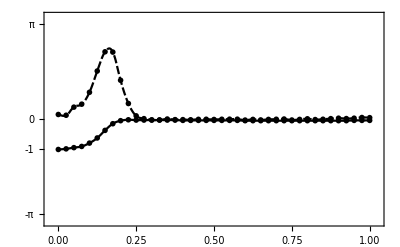

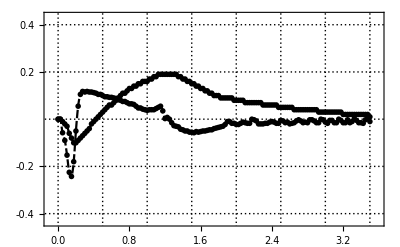

```mathematica
data = {
Import[NotebookDirectory[]<>"../../data/good-theta-max/.8.csv"],
Import[NotebookDirectory[]<>"../../data/good-theta-max/.9.csv"],
Import[NotebookDirectory[]<>"../../data/good-theta-max/1.csv"]
} ;

time179 = Table[.025*i, {i, 0, 178, 1}];

ltheta1 =  Transpose[data[[3]]][[1;;4]] * { 1, 1/4,1, 1/4};
ltheta1[[1]] //Length
 thetaPlot1 = ListLinePlot[
{
Transpose[{
time179,
ltheta1[[3]]
}][[1;;41]],
Transpose[{
time179,
ltheta1[[4]]
}][[1;;41]]
},
InterpolationOrder->2,
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
FrameTicksStyle->Directive[FontSize->16],
FrameLabel ->{MaTeX["\\text{Tempo }(s)",Magnification->1.5]},
PlotLegends->{MaTeX["\\theta",Magnification->1.5],MaTeX["\\dot \\theta \\left(s^{-1} / 4\\right)",Magnification->1.5]},
FrameTicks->{{{-Pi, Pi, -1, 0}, None}, {Automatic, None}},
PlotRange->{{-.025, 1.025},{-Pi-.25, Pi+.25}},
GridLines->{{-.03, 0, .2, .4, .6, .8, 1}, {0,-1, Pi, -Pi}}
]

xPlot1 = ListLinePlot[{
Transpose[{
time179,
ltheta1[[1]]
}][[1;;141]],
Transpose[{
time179,
ltheta1[[2]]
}][[1;;141]]
},
InterpolationOrder->2,
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
FrameTicksStyle->Directive[FontSize->16],
FrameLabel ->{MaTeX["\\text{Tempo }(s)",Magnification->1.5]},
PlotLegends->{MaTeX["q(m)",Magnification->1.5],MaTeX["\\dot q \\left(ms^{-1}/ 4\\right) ",Magnification->1.5]},
PlotRange->{{-.085, 3.585},{-.435, .435}},
FrameTicks->{{{-.4, .4, .2, -.2}, None}, {Automatic, None}},
GridLines->{{-.25, 0, .5, 1, 1.5, 2, 2.5, 3, 3.5}, {0, .2, -.2, -.4, .4}}
]
```

```mathematica
Export[NotebookDirectory[]<>"../theta-limit-angle8.pdf",thetaPlot8,"PDF"]
Export[NotebookDirectory[]<>"../theta-limit-pos8.pdf",xPlot8,"PDF"]
Export[NotebookDirectory[]<>"../theta-limit-angle9.pdf",thetaPlot9,"PDF"]
Export[NotebookDirectory[]<>"../theta-limit-pos9.pdf",xPlot9,"PDF"]
Export[NotebookDirectory[]<>"../theta-limit-angle1.pdf",thetaPlot1,"PDF"]
Export[NotebookDirectory[]<>"../theta-limit-pos1.pdf",xPlot1,"PDF"]
```

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../theta-limit-angle8.pdf

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../theta-limit-pos8.pdf

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../theta-limit-angle9.pdf

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../theta-limit-pos9.pdf

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../theta-limit-angle1.pdf

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../theta-limit-pos1.pdf

```mathematica
data = Transpose[Import[NotebookDirectory[]<>"../../data/good-stabilization/run.csv"][[2;;211]]];

time225 = Table[.025*i, {i, -9, 200, 1}];

xPlot = ListPlot[
Transpose[{
time225,
data[[1]]
}],
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid", "Large"},
FrameTicksStyle->Directive[FontSize->16],
PlotMarkers->None,
InterpolationOrder->1,
PlotLegends->{MaTeX["\\text{Dati reali}",Magnification->1.5]},
FrameLabel->{MaTeX["\\text{Tempo }(s)",Magnification->1.5],MaTeX["q\\ (m)",Magnification->1.5]},
PlotRange->{{-.35, 5.1},{-.42, .42}},
FrameTicks->{{{-.4, .4, .2, -.2}, None}, {Automatic, None}},
GridLines->{{-.25, 0, 1, 2, 3, 4, 5}, {0, .2, -.2, -.4, .4}}
];

vPlot = ListPlot[
Transpose[{
time225,
data[[2]]
}],
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid", "Large"},
FrameTicksStyle->Directive[FontSize->16],
PlotMarkers->None,
InterpolationOrder->1,
PlotLegends->{MaTeX["\\text{Dati reali}",Magnification->1.5]},
FrameLabel->{MaTeX["\\text{Tempo }(s)",Magnification->1.5],MaTeX["\\dot q\\ (m/s)",Magnification->1.5]},
PlotRange->{{-.35, 5.1},{-1, 1}},
FrameTicks->{{{-1, 1, .5, -.5}, None}, {Automatic, None}},
GridLines->{{-.25, 0, 1, 2, 3, 4, 5}, {0,-1, 1, .5, -.5}}
];

aPlot = ListPlot[
Transpose[{
time225,
data[[3]]
}],
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid", "Large"},
FrameTicksStyle->Directive[FontSize->16],
InterpolationOrder->1,
PlotLegends->{MaTeX["\\text{Dati reali}",Magnification->1.5]},
FrameLabel->{MaTeX["\\text{Tempo }(s)",Magnification->1.5],MaTeX["\\theta",Magnification->1.5]},
PlotRange->{{-.35, 5.1},{-Pi/8, Pi/8}},
FrameTicks->{{{-Pi/8, Pi/8, Pi/16, -Pi/16}, None}, {Automatic, None}},
GridLines->{{-.25, 0, 1, 2, 3, 4, 5}, {0, Pi/16, -Pi/16}}
];

wPlot = ListPlot[
Transpose[{
time225,
data[[4]]
}],
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid", "Large"},
FrameTicksStyle->Directive[FontSize->16],
PlotLegends->{MaTeX["\\text{Dati reali}",Magnification->1.5]},
FrameTicksStyle->Directive[FontSize->13],
FrameLabel->{MaTeX["\\text{Tempo }(s)",Magnification->1.5],MaTeX["\\dot \\theta\\ (s^{-1})",Magnification->1.5]},
PlotRange->{{-.35, 5.1},{-Pi, Pi}},
FrameTicks->{{{-Pi, Pi, Pi/2, -Pi/2}, None}, {Automatic, None}},
GridLines->{{-.25, 0, 1, 2, 3, 4, 5}, {0, Pi/2, -Pi/2}}
];

{xPlot, vPlot, aPlot, wPlot};
```

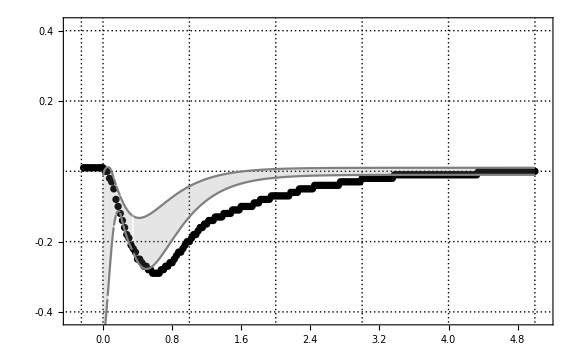
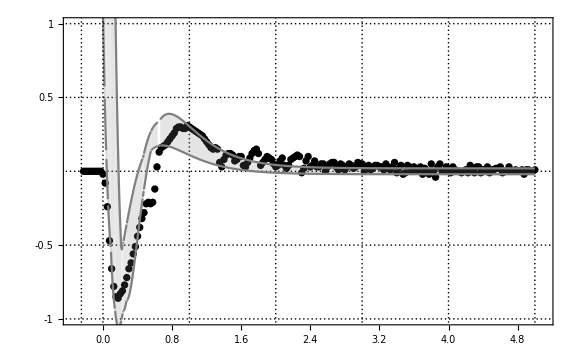
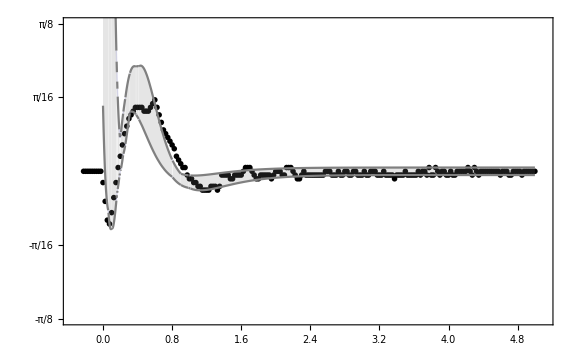
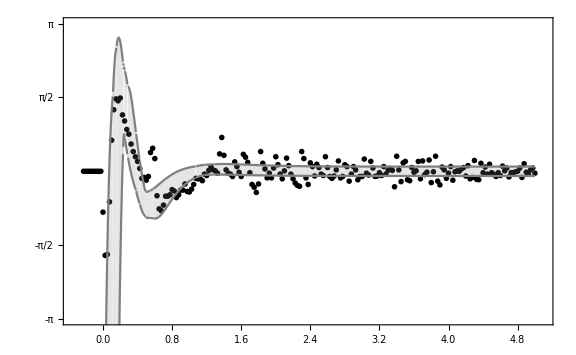

```mathematica
s[t_]:= {x[t],  x'[t], θ[t], θ'[t] };
T = 5;

Klqr = LQRegulatorGains[ssm /. params, {Q, R} /. params];
allFunctions = Transpose[
Table[ 
simulateSystem[-Klqr.s[t], T, Transpose[data][[c]], 0, .025*(c-9)],
 {c, 11, 19, 1}
]
];

fMax[i_] := Max[
allFunctions[[i]]
];
fMin[i_] := Min[
allFunctions[[i]]
];

opt1 = Plot[{
fMax[1] + .01,
fMin[1]-.01
},
{t, 0, T},
Filling->{1->{2}},
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid", "Large"},
PlotRange->{{-.5, 5},Full},
PlotLegends->{MaTeX["\\text{Traiettoria prevista}",Magnification->1.5]},
FrameTicksStyle->Directive[FontSize->13],
FrameLabel ->{MaTeX["\\text{Tempo }(s)",Magnification->1.5], MaTeX["\\text{Costo istantaneo}",Magnification->1.5]},
PlotStyle->{{Gray, Dashing[None]},{Gray, Dashing[None]}}
];
opt2 = Plot[{
fMax[2] + .02,
fMin[2]-.02
},
{t, 0, T},
Filling->{1->{2}},
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
PlotRange->{{-.5, 5},Full},
PlotLegends->{MaTeX["\\text{Traiettoria prevista}",Magnification->1.5]},
FrameTicksStyle->Directive[FontSize->13],
FrameLabel ->{MaTeX["\\text{Tempo }(s)",Magnification->1.5], MaTeX["\\text{Costo istantaneo}",Magnification->1.5]},
PlotStyle->{{Gray, Dashing[None]},{Gray, Dashing[None]}}
];
opt3 = Plot[{
fMax[3] + .01,
fMin[3]-.01
},
{t, 0, T},
Filling->{1->{2}},
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
PlotRange->{{-.5, 5},Full},
PlotLegends->{MaTeX["\\text{Traiettoria prevista}",Magnification->1.5]},
FrameTicksStyle->Directive[FontSize->13],
FrameLabel ->{MaTeX["\\text{Tempo }(s)",Magnification->1.5], MaTeX["\\text{Costo istantaneo}",Magnification->1.5]},
PlotStyle->{{Gray, Dashing[None]},{Gray, Dashing[None]}}
];
opt4 = Plot[{
fMax[4] + .1,
fMin[4]-.1
},
{t, 0, T},
Filling->{1->{2}},
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
PlotRange->{{-.5, 5},Full},
PlotLegends->{MaTeX["\\text{Traiettoria prevista}",Magnification->1.5]},
FrameTicksStyle->Directive[FontSize->13],
FrameLabel ->{MaTeX["\\text{Tempo }(s)",Magnification->1.5], MaTeX["\\text{Costo istantaneo}",Magnification->1.5]},
PlotStyle->{{Gray, Dashing[None]},{Gray, Dashing[None]}}
];

fancyPlots = {
Show[xPlot, opt1],
Show[vPlot, opt2],
Show[aPlot, opt3],
Show[wPlot, opt4]
}
```

```mathematica
Export[NotebookDirectory[]<>"../x-plot.pdf",fancyPlots[[1]],"PDF"]
Export[NotebookDirectory[]<>"../v-plot.pdf",fancyPlots[[2]],"PDF"]
Export[NotebookDirectory[]<>"../a-plot.pdf",fancyPlots[[3]],"PDF"]
Export[NotebookDirectory[]<>"../w-plot.pdf",fancyPlots[[4]],"PDF"]
```

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../x-plot.pdf

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../v-plot.pdf

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../a-plot.pdf

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../w-plot.pdf

## Grafici swingup

Per usare questi grafici è necessario aprire il "notebook dei calcoli"/Users/matteo/repo/uni/dpic/docs/report/assets/source/calcoli.nbNone/Users/matteo/repo/uni/dpic/docs/report/assets/source/calcoli.nb ed eseguire il codice, in modo che siano definite le funzioni corrette.

0.0243628 (-1+Cos[θ[t]])+0.00018 θ'[t]^2

20 Tanh[Cos[θ[t]] θ'[t] (0.0243628 (-1+Cos[θ[t]])+0.00018 θ'[t]^2)]

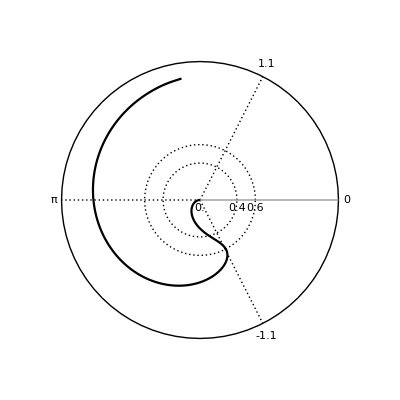

```mathematica
s[t_]:= {x[t],  x'[t], θ[t], θ'[t] };
T = .75;

K = LQRegulatorGains[ssm /. params, {Q, R} /. {r11->.05, q11->2}/. params];
En=1/2 J θ'[t]^2+m g l (Cos[θ[t]]-1)/. params
aMax=20;
lyap=aMax Tanh[En Cos[θ[t]] θ'[t]]

solutionsSwup=simulateSystem[lyap,T,{0,0,Pi,.1}];
force=0;D[solutionsLQR[[1]],t];



 polarSwup = ListPolarPlot[{
Table[{
Evaluate[solutionsSwup[[3]]],
Evaluate[solutionsSwup[[1]]]
}, {t, 0, T, .01}
]
},
InterpolationOrder->2,
Joined->True,
PlotRange->{{-Pi/2 - .2, Pi/2+.2},{-Pi/2-.2, Pi/2+.2}},
PlotTheme->{"Monochrome", "SerifLabels"},
PlotLegends->{MaTeX["\\left(q(t), \\theta(t)\\right)",Magnification->1.5],MaTeX["\\theta_{LQR}",Magnification->1.5]},
PolarGridLines->{{1.1,-1.1, Pi},{.4, .6}},
PolarAxes->{True, True},
PolarAxesOrigin->{0, 1.3},
PolarTicks->{{ 1.1, -1.1, Pi, 0}, {0, .4, .6}}
]
```

```mathematica
Export[NotebookDirectory[]<>"../polar-swingup-simulation.pdf",polarSwup,"PDF"]
```

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../polar-swingup-simulation.pdf

0.0243628 (-1+Cos[θ[t]])+0.00018 θ'[t]^2

20 Tanh[Cos[θ[t]] θ'[t] (0.0243628 (-1+Cos[θ[t]])+0.00018 θ'[t]^2)]

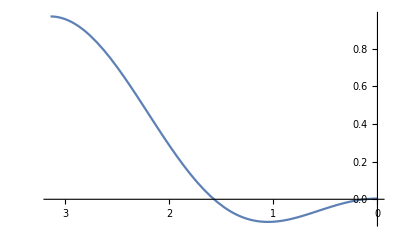

```mathematica
s[t_]:= {x[t],  x'[t], θ[t], θ'[t] };
T = .75;

K = LQRegulatorGains[ssm /. params, {Q, R} /. {r11->.05, q11->2}/. params];
En=1/2 J θ'[t]^2+m g l (Cos[θ[t]]-1)/. params
aMax=20;
lyap=aMax Tanh[En Cos[θ[t]] θ'[t]]

solutionsSwup=simulateSystem[lyap*En Cos[θ[t]] θ'[t],T,{0,0,Pi,.1}];
force=0;D[solutionsLQR[[1]],t];

Plot[lyap /. θ'[t] ->1, {θ[t], Pi, 0}, ScalingFunctions->{"Reverse",None}]
```

```mathematica
ClearAll[arcsWArrows];
arcsWArrows[args1:{{_,{_,_}}..},dir_List:{Directive[GrayLevel[.3],Arrowheads[{{0.05,1}}]]}]:=ParametricPlot[Evaluate[#[[1]]*{Cos[Rescale[u,{0,2 Pi},Abs@#[[2]]]],Sin[Rescale[u,{0,2 Pi},Abs@#[[2]]]]}&/@args1],{u,0,2 Pi},PlotStyle->dir,Axes->False,PlotRangePadding->.2,ImageSize->200]/. Line[x_,___]:>Arrow[x]
```

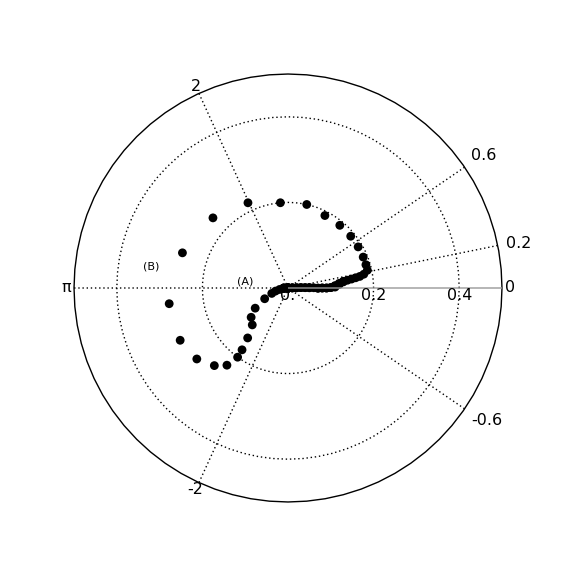

```mathematica
data = Transpose[Import[NotebookDirectory[]<>"../../data/good-swingup/swingup-fast-single.csv"]];

arr1 = arcsWArrows[{{.4,{Pi+.3, Pi-.9}}}];
arr2 = arcsWArrows[{{.1,{ Pi/2, Pi}}}];
 polarSwupR = ListPolarPlot[{
Transpose[{ data[[3]],data[[1]] }]
},
InterpolationOrder->2,
Joined->False,
PlotTheme->{"Monochrome", "SerifLabels",  "Large"},
PlotLegends->{MaTeX["\\left(q(t), \\theta(t)\\right)",Magnification->1.5]},
PolarGridLines->{{2, -2, .6, -.6, .2 , Pi},{.4, .6, .2}},
PolarAxes->{True, True},
PolarTicks->{{ 2, -2, Pi, 0, .6, -.6, .2}, {0, .4, .6, .2}},
Epilog->{ 
Inset[arr1, {-.25, 0.03}],
Inset[arr2, {-.06, -.03}],
Inset[Text[Style["(A)", 16]], {-.1, .015}],
Inset[Text[Style["(B)", 16]], {-.32, .05}]
},
PlotRange->{{-.55, .55},{-.55, .55}},
PolarAxesOrigin->{0, .41},
TicksStyle->Directive[FontSize->16],
AxesStyle->Directive[Thick]
]
```

```mathematica
Export[NotebookDirectory[]<>"../polar-swingup-real.pdf", polarSwupR,"PDF"]
```

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../polar-swingup-real.pdf

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

-0.0471405 √(60907.+2.5×10^6 a-60907. Cos[θ[t]])

-ArcCos[2.64185-0.00738831 r]

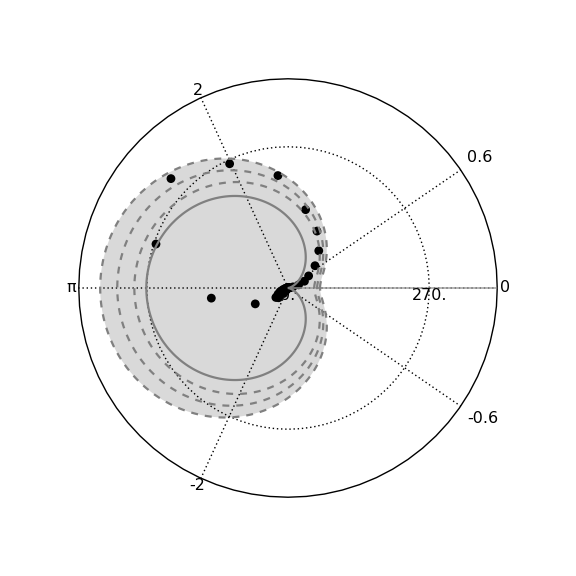

```mathematica
data = Transpose[Import[NotebookDirectory[]<>"../../data/good-swingup/swingup-fast-single.csv"]]; 
energyReal = ListPolarPlot[{
Transpose[{ data[[3]],(data[[4]] )^2}]
},
InterpolationOrder->2,
Joined->False,
Mesh->None,
PlotTheme->{"Monochrome", "SerifLabels",  "Large"},
PlotLegends->{MaTeX["\\left(\\dot \\theta^2(t), \\theta(t)\\right)", Magnification->1.5]},
PolarGridLines->{{ .6, -.6, 0, 2, -2, Pi}, {270}},
PolarAxes->{True, True},
PolarTicks->{{0, .6, -.6, 2, -2, Pi}, {0, 270}},
Epilog->{ 
},
PlotRange->{{-450, 450},{-450, 450}},
PolarAxesOrigin->{0, 400},
TicksStyle->Directive[FontSize->16],
AxesStyle->Directive[Thick]
];

Solve[En == a, {θ'[t]}][[1, 1, 2]]
IPM = -ArcCos[1. +41.046185167550526 (.04)-0.007388313330159095r]

cardioid1= PolarPlot[{
Interpolation[Table[{a, (135.49 +5555  (0.01)-135.35 Cos[a])*1.1}, {a, 0, 2Pi, .01}]][c],
Interpolation[Table[{a, (135.49 +5555  (0.01)-135.35 Cos[a])*.9}, {a, 0, 2Pi, .01}]][c],
Interpolation[Table[{a, (135.49 +5555  (0.01)-135.35 Cos[a])*1}, {a, 0, 2Pi, .01}]][c],
Interpolation[Table[{a, (135.49 +5555  (0.0)-135.35 Cos[a])*1}, {a, 0, 2Pi, .01}]][c]
},{c, 0, 2Pi},
PlotTheme->{"Monochrome", "SerifLabels",  "Large"},
PlotLegends->{
None,
None,
 MaTeX["\\text{Energia obiettivo}", Magnification->1.5],
MaTeX["\\text{Energia a }\\mathbf x = \\mathbf 0", Magnification->1.5]
},
PolarAxes->{False, False},
TicksStyle->Directive[FontSize->16],
AxesStyle->Directive[Thick],
PlotStyle->{{Gray, Dashed},{Gray, Dashed}, {Gray, Dashed},{Gray, Dashing[None]}}
];

polarEnergy = Show[energyReal, cardioid1, Prolog->{LightGray,FilledCurve[Cases[cardioid1,_Line, All][[1;;2]]]}]
```

```mathematica
Export[NotebookDirectory[]<>"../polar-swingup-energy.pdf",polarEnergy,"PDF"]
```

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../polar-swingup-energy.pdf